# Behavior

```mathematica
cd=ColorData[97,"ColorList"];
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
dir ="../AnalysisData/best_categ_pass_agent/";
dir = "../AnalysisData/best_offset/";
```

## Task 1: Object Recognition

```mathematica
ba=Import[ StringJoin[dir,"B_avoid_aposx.dat"]];
bc=Import[ StringJoin[dir,"B_catch_aposx.dat"]];
aa=Import[ StringJoin[dir,"A_avoid_aposx.dat"]];
ac=Import[ StringJoin[dir,"A_pass_aposx.dat"]];
```

```mathematica
Show[{ListLinePlot[ba,PlotRange->All,PlotStyle->cd[[1]]],ListLinePlot[bc,PlotRange->All,PlotStyle->cd[[2]]]},PlotRange->{Automatic,{-30,30}},Frame->True,FrameLabel->{"Time","Offset"},ImageSize->250]
Export["Behavior.eps",%]
```

-Graphics-

Behavior.eps

```mathematica
Show[{ListLinePlot[ba,PlotRange->All,PlotStyle->cd[[1]]],ListLinePlot[bc,PlotRange->All,PlotStyle->cd[[2]]]},PlotRange->{Automatic,{-25,25}},Frame->True,FrameLabel->{"Time","Offset"},ImageSize->250]
Export["Behavior.eps",%]
```

-Graphics-

Behavior.eps

## Task 1: Object Recognition

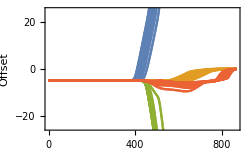

Behavior.eps

```mathematica
Show[{ListLinePlot[ba,PlotRange->All,PlotStyle->cd[[1]]],ListLinePlot[bc,PlotRange->All,PlotStyle->cd[[2]]],ListLinePlot[aa,PlotRange->All,PlotStyle->cd[[3]]],ListLinePlot[ac,PlotRange->All,PlotStyle->cd[[4]]]},PlotRange->{Automatic,{-25,25}},Frame->True,FrameLabel->{"Time","Offset"},ImageSize->250]

Export["Behavior.eps",%]
```